```mathematica
path=NotebookDirectory[]<>"data/";
```

```mathematica
file[type_,n_]:=Flatten@Import[path<>"entropy_"<>type<>"_Npts"<>ToString[n]<>"_Nsim100000.csv"]
```

```mathematica
ns = {100,1000,10000,100000,1000000};
```

```mathematica
teo1[t_]:=Which[
t=="exc",-EulerGamma/2,
t=="brd",-(EulerGamma+2)/2,
True, 0
]
teo2[t_]:=Which[
t=="exc",EulerGamma^2/4 + 5 Pi^2/24-2,
t=="brd",4/3+EulerGamma^2/4 + EulerGamma-Pi^2/72 ,
True, 0
]
```

```mathematica
comparison=Table[
data=file[t,n]/n-1/2Log[n];
{Mean[data]/teo1[t],Moment[data,2]/teo2[t]}
,{t,{"exc","brd"}},{n,ns}]
```

{{{1.20582,1.32106},{1.08169,1.12194},{1.02578,1.03516},{1.00775,1.01394},{1.00145,1.00161}},{{0.773462,0.60116},{0.904419,0.818295},{0.961433,0.924013},{0.984721,0.969996},{0.994687,0.989417}}}

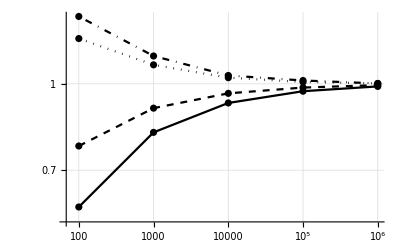

```mathematica
img0=ListLogLogPlot[Transpose@{ns,#}&/@{comparison[[1,;;,1]],comparison[[1,;;,2]],comparison[[2,;;,1]],comparison[[2,;;,2]]}, Joined->True ,Mesh->All,PlotStyle->{{GrayLevel[0],Dotted},{GrayLevel[0],DotDashed},{GrayLevel[0],Dashed},{GrayLevel[0]}}, PlotLegends->{"\n","\n","\n","\n"},GridLines->Automatic]
```

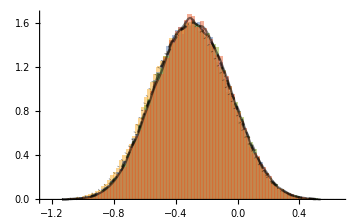

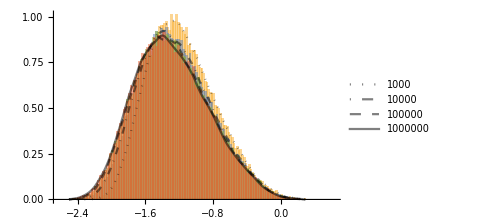

```mathematica
img1=Show[
Histogram[(file["exc",#]-(#/2( Log[#])  ))/#&/@ns[[2;;]],100,"PDF",ChartStyle-> Opacity[0.5],ImageSize->Medium,TicksStyle->Medium],
SmoothHistogram[(file["exc",#]-(#/2( Log[#])  ))/#&/@ns[[2;;]],Automatic,"PDF",PlotStyle->{
{Opacity[0.5],GrayLevel[0],Dotted},
{Opacity[0.5],GrayLevel[0],DotDashed},
{Opacity[0.5],GrayLevel[0],Dashed},
{Opacity[0.5],GrayLevel[0]}
}]
]
img2=Show[
Histogram[(file["brd",#]-(#/2( Log[#])  ))/#&/@ns[[2;;]],100,"PDF",ChartStyle-> Opacity[0.5],ImageSize->Medium,TicksStyle->Medium],
SmoothHistogram[(file["brd",#]-(#/2( Log[#])  ))/#&/@ns[[2;;]],Automatic,"PDF",PlotStyle->{
{Opacity[0.5],GrayLevel[0],Dotted},
{Opacity[0.5],GrayLevel[0],DotDashed},
{Opacity[0.5],GrayLevel[0],Dashed},
{Opacity[0.5],GrayLevel[0]}
},PlotLegends->ns[[2;;]]]
]
```